```mathematica
(*4a*)
```

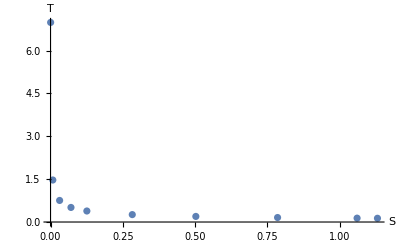

```mathematica
X1=ListPlot[Table[{Con1[[i]][[1]]^2 Pi,Con1[[i]][[5]]}, {i, 1,10}], PlotRange->All,AxesLabel->{Style[" S",FontSize->18],Style["T", FontSize->18]}]
```

```mathematica
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,Length[Con1]}];
```

```mathematica
FindFit[MS1,a0 + a1 x^a2 ,{a0,a1,a2},x]
```

{a0→0.023501,a1→0.274575,a2→0.517725}

```mathematica
MMSS1=a0 + a1 x^a2/.%
```

```mathematica
MMSS1=0.023501+0.2745748031661924 x^0.5177245713714081
```

0.023501+0.274575 x^0.517725

```mathematica
D[0.023501+0.2745748031661924 x^0.5177245713714081,x]
```

0.142154/x^0.482275

```mathematica
XP=Plot[0.14215412227860574/x^0.48227542862859185,{x,0.0003,1.2},PlotRange->All]
```

```mathematica
dmds1=Table[0.14215412227860574/x^0.48227542862859185/. x->Con1[[i]][[1]]^2 Pi, {i,1,10}]
```

{6.95181,1.47199,0.754305,0.51015,0.386535,0.26142,0.198075,0.159718,0.138185,0.133962}

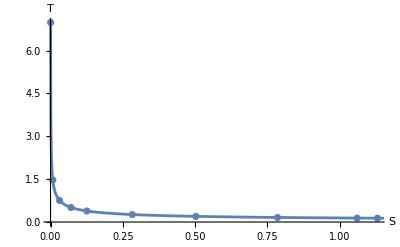

```mathematica
Show[X1,XP]
```

```mathematica
(*4b*)
```

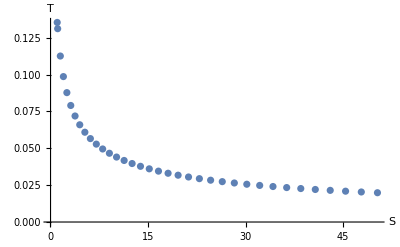

```mathematica
X3=ListPlot[Table[{Con1[[i]][[1]]^2 Pi,Con1[[i]][[5]]}, {i, 9,44}], PlotRange->All,AxesLabel->{Style[" S",FontSize->18],Style["T", FontSize->18]}]
```

```mathematica
Length[Con1]
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,Length[Con1]-3,Length[Con1]}]
```

```mathematica
MSN1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]},{i,1,Length[Con1]}];
```

```mathematica
FindFit[MS1, Sqrt[x/(4 Pi)]+ a1/x^a2 ,{a1,a2},x]
```

```mathematica
{a1->0.014956783680758215,a2->0.16081197973238245}
```

{a1→0.0149568,a2→0.160812}

```mathematica
Sqrt[x/(4 *Pi)]+ a1/x^a2/.%
```

```mathematica
Ms1=0.014956783680758215/x^0.16081197973238245+(√x)/(2 √π)
```

0.0149568/x^0.160812+(√x)/(2 √π)

```mathematica
D[Ms1,x]
```

-0.00240523/x^1.16081+1/(4 √π √x)

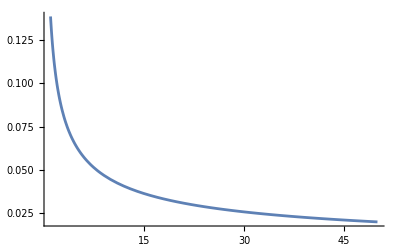

```mathematica
XPP=Plot[-0.002405229994131719/x^1.1608119797323824+1/(4 √π √x),{x,1,50},PlotRange->All]
```

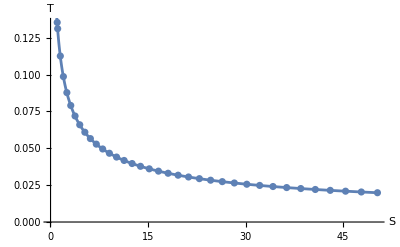

```mathematica
Show[X3,XPP]
```

```mathematica
dmds2=Table[-0.002405229994131719/x^1.1608119797323824+1/(4 √π √x)/. x->Con1[[i]][[1]]^2 Pi, {i,9,44}]
```

{0.13472,0.130544,0.112224,0.0984027,0.087606,0.0789406,0.0718327,0.0658975,0.0608671,0.0565494,0.0528032,0.049522,0.0466245,0.044047,0.0417394,0.0396613,0.0377803,0.0360695,0.0345068,0.0330738,0.0317551,0.0305374,0.0294097,0.0283622,0.0273867,0.0264761,0.0256241,0.0248252,0.0240746,0.023368,0.0227017,0.0220723,0.0214769,0.0209127,0.0203775,0.0198689}